# Parallels

—Clayton Shonkwiler, June 2025.

Consider the hyperbolic plane ℍ^2, realized in the Poincaré half-plane model. We can interpret this as the upper half-plane {(x,y) ∈ℝ^2: y > 0} together with the Riemannian metric ⅆ s^2=1/y^2(ⅆ x^2+ⅆ y^2).

In other words, if U=u_1∂/(∂x)+u_2∂/(∂y),V=v_1∂/(∂x)+v_2∂/(∂x)∈T_(x,y)ℍ^2, then

	⟨U,V⟩_(x,y)=(u_1 v_1)/y^2+(u_2 v_2)/y^2=1/y^2(u_1 v_1+u_2 v_2).

Therefore, if ∇ is the Levi-Civita connection associated with this Riemannian metric, one can check that, using the notation X=∂/(∂x) and Y=∂/(∂y),

	∇_X X=1/y Y,	∇_X Y=∇_Y X=-1/yX, 		∇_Y Y=-1/yY.

For more details, see Example 4.3.10 in my differential geometry notes.

Now, consider the curve α(t)=(y_0 t,y_0) for some fixed y_0>0. This is a horocycle centered at y=∞. It’s parametrized by arclength since α'(t)=y_0 X, which is a unit vector since ∥y_0 X∥^2=⟨y_0 X,y_0 X⟩_(y_0 t,y_0)=y_0^2/y_0^2=1.

If we want to parallel translate a tangent vector W_0 at, say, α(0)=(0,y_0), then we get a vector field W(t)=a(t)X+b(t)Y along the curve which satisfies the differential equation

	0 = (D W)/ⅆt=∇_(α'(t)) W(t)=∇_(y_0 X) W(t).
	
Here D/ⅆt is the covariant derivative along the curve α.

Expanding this out a bit, we see that

	0=∇_(y_0 X) W(t)=∇_(y_0 X) (a(t)X+b(t)Y)=y_0[a'(t)X+a(t)∇_X X+b'(t)Y+b(t)∇_X Y]=y_0[(a'(t)-(b(t))/y_0)X+(b'(t)+(a(t))/y_0)Y].

X and Y form a basis for the tangent space at each point, so the only way for this equation to be satisfied is if both coefficients are zero, meaning that the parallel transport equation is the system of ODEs

	a'(t)-(b(t))/y_0=0
b'(t)+(a(t))/y_0=0.

If we want W_0 to be the unit vector y_0 Y∈T_(0,y_0)ℍ^2, then we have the initial conditions a(0)=0,b(0)=y_0.

Mathematica will happily solve this initial value problem:

```mathematica
DSolve[{a'[t]-b[t]/Subscript[y, 0]==0,b'[t]+a[t]/Subscript[y, 0]==0,a[0]==0,b[0]==Subscript[y, 0]},{a,b},t]
```

{{a→Function[{t},Sin[t/y_0] y_0],b→Function[{t},Cos[t/y_0] y_0]}}

Here’s a visualization showing the resulting parallel fields when y_0=1/2,1,2:

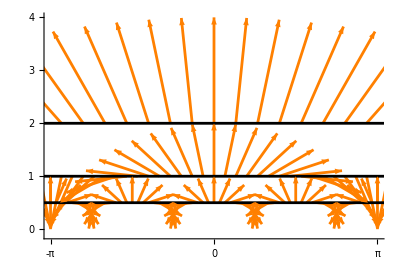

```mathematica
Graphics[Table[{Black,Thickness[.005],InfiniteLine[{{0,y0},{1,y0}}],Orange,Table[Arrow[{{y0 t,y0},{y0 t,y0}+y0{Sin[t/y0],Cos[t/y0]}}],{t,-4π,4π,2π/30}]},{y0,{1/2,1,2}}],PlotRange->{{-π,π},{-.1,4}},Axes->True,Ticks->{Range[-π,π,π],Range[0,4]}]
```

A parallel vector field is always pointing in the same direction from the perspective of someone inside the manifold, so the way to interpret this is that a person traversing the curve α(t)=(y_0 t,y_0) is constantly turning to the left to stay on α. This makes sense: the geodesics (which are the straight paths) are vertical lines and semi-circles centered at points on the x-axis, so at each point going “straight ahead” would mean walking along the semi-circle tangent to α at that point. So to stay on α you have to turn (to the left!) away from that semi-circle.

Now we start to turn this into an animation. In all of what follows, we’ll use y_0=2/3 (based on the value of this parameter that I thought gave good results in the final animation).

The arrows look a little bit too mathy, so let’s show the corresponding line field instead:

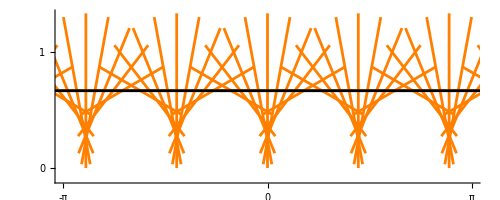

```mathematica
With[{y0=2/3},
Graphics[{Black,Thickness[.005],InfiniteLine[{{0,y0},{1,y0}}],Orange,Table[Line[{{y0 t,y0}-y0{Sin[t/y0],Cos[t/y0]},{y0 t,y0}+y0{Sin[t/y0],Cos[t/y0]}}],{t,-2π,2π,2π/30}]},PlotRange->{{-π,π},{-.1,4/3}},Axes->True,Ticks->{Range[-π,π,π],Range[0,1]}]
]
```

Which we can animate:

```mathematica
With[{y0=2/3},
Animate[Graphics[{Black,Thickness[.005],InfiniteLine[{{0,y0},{1,y0}}],Orange,Table[Line[{{y0 s,y0}-y0{Sin[s/y0],Cos[s/y0]},{y0 s,y0}+y0{Sin[s/y0],Cos[s/y0]}}],{s,-2π+t,2π+t,2π/30}]},PlotRange->{{-π,π},{-.1,4/3}},Axes->True,Ticks->{Range[-π,π,π],Range[0,4]}],{t,0,2π/30},SaveDefinitions->True]
]
```

Let’s make this look a little more pleasant by shortening the lines, getting rid of the axes and underlying curve, and using some different colors (taken from this ColorHunt palette):

```mathematica
With[{y0=2/3,cols=RGBColor/@{"#384B70","#FCFAEE"}},
Animate[Graphics[{CapForm["Round"],Thickness[.0025],cols[[1]],Table[Line[{{y0 s,y0}-y0/8{Sin[s/y0],Cos[s/y0]},{y0 s,y0}+y0/8{Sin[s/y0],Cos[s/y0]}}],{s,-2π+t,2π+t,2π/60}]},PlotRange->{{-2,2},{0,4/3}},Background->cols[[2]],ImageSize->600],{t,0,2π/60},SaveDefinitions->True]
]
```

To produce the final animation, we’re going to transform the curve α (which remember was a horocycle centered at y=∞) to a horocycle centered at a finite point on the x-axis.

Recall that the Cayley transform f(z)=(z-ⅈ)/(z+ⅈ) maps the upper half-plane model to the Poincaré disk model, and of course its inverse f^-1(z)=ⅈ(1+z)/(1-z) goes the other way:

```mathematica
Cayley[z_]:=(z-I)/(z+I);
CayleyInverse[z_]:=I(1+z)/(1-z);
```

Therefore, the Cayley transform sends our horocycle α(t)=(y_0 t,y_0) to the horocycle pictured below:

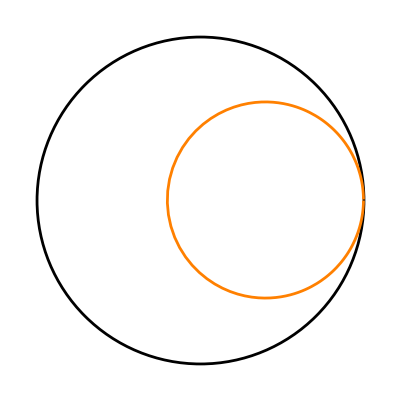

```mathematica
With[{y0=2/3},
Show[
Graphics[{Thickness[.005],Circle[]}],
ParametricPlot[ReIm[Cayley[Complex@@{y0 t,y0}]],{t,-1000,1000},PlotStyle->Orange,PlotPoints->200]]
]
```

But now we can get a horocycle centered at a different point by just rotating (say by 90.ba clockwise, which we can do by multiplying by -ⅈ):

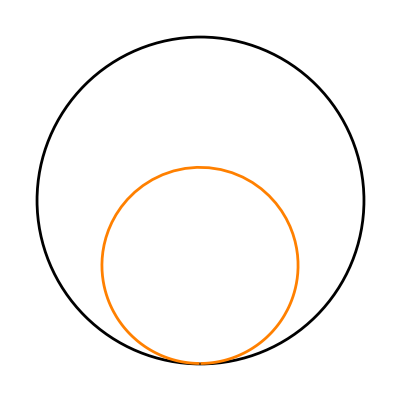

```mathematica
With[{y0=2/3},
Show[
Graphics[{Thickness[.005],Circle[]}],
ParametricPlot[ReIm[-I*Cayley[Complex@@{y0 t,y0}]],{t,-1000,1000},PlotStyle->Orange,PlotPoints->200]]
]
```

And then we get back into the upper half-plane model by applying the inverse of the Cayley transform:

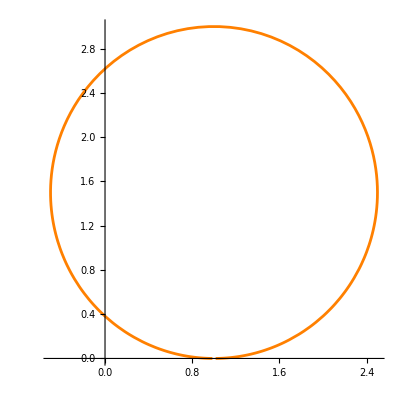

```mathematica
With[{y0=2/3},
ParametricPlot[ReIm[CayleyInverse[-I*Cayley[Complex@@{y0 t,y0}]]],{t,-200,200},PlotStyle->Orange,PlotPoints->200,PlotRange->All]
]
```

(In retrospect, I should have multiplied by -1 rather than -ⅈ, but I don’t want to try to recreate the final product with that change in parameters.)

Here’s our line field from before, fed through this transformation (strictly speaking, I should really be applying the differential of the map to the vector field, but that requires more work):

```mathematica
With[{y0=2/3,cols=RGBColor/@{"#384B70","#FCFAEE"}},
Animate[Graphics[{CapForm["Round"],Thickness[.005],cols[[1]],Table[Line[{ReIm[CayleyInverse[-I*Cayley[Complex@@({y0 s,y0}-y0/8{Sin[s/y0],Cos[s/y0]})]]],ReIm[CayleyInverse[-I*Cayley[Complex@@({y0 s,y0}+y0/8{Sin[s/y0],Cos[s/y0]})]]]}],{s,-20π-3/2+t,20π-3/2+t,2π/60}]},PlotRange->{{-1.75,3.75},{-1,4.5}},Background->cols[[2]],ImageSize->500],{t,0,2π/60},SaveDefinitions->True]
]
```

Two more changes will give us the final animation. First, I’m going to apply a global rotation by an angle θ=1.36 to the line field (this gave a result I was happier with). Second, I’m going to scale the thickness of the line segments by the height of the point they’re based at (recall that the Riemannian metric is ⅆ s^2=1/y^2(ⅆ x^2+ⅆ y^2), so scaling by y keeps length constant; that is, I’m visualizing this line field with constant-length segments in the hyperbolic metric).

The point (y_0 s,y_0)=y_0 s+ⅈ y_0 gets sent to the point

```mathematica
ComplexExpand[FullSimplify[CauchyInverse[-I*Cauchy[Subscript[y, 0] s+I Subscript[y, 0]]]]]
```

1-2/(y_0^2+(1+s y_0)^2)+(2 ⅈ y_0)/(y_0^2+(1+s y_0)^2)-(2 s y_0)/(y_0^2+(1+s y_0)^2)

which has imaginary part (i.e., height) equal to (2 y_0)/(y_0^2+(1+s y_0)^2), so this is the scale factor for thickness.

```mathematica
With[{y0=2/3,θ=1.36,cols=RGBColor/@{"#384B70","#FCFAEE"}},
Animate[Graphics[{CapForm["Round"],cols[[1]],Table[{Thickness[(2 y0)/(y0^2+(1+s y0)^2)*.0025],Line[{ReIm[CayleyInverse[-I*Cayley[Complex@@({y0 s,y0}-y0/8{Sin[s/y0+θ],Cos[s/y0+θ]})]]],ReIm[CayleyInverse[-I*Cayley[Complex@@({y0 s,y0}+y0/8{Sin[s/y0+θ],Cos[s/y0+θ]})]]]}]},{s,-20π-3/2+t,20π-3/2+t,2π/60}]},PlotRange->{{-1.75,3.75},{-1,4.5}},Background->cols[[2]],ImageSize->500],{t,0,2π/60},SaveDefinitions->True]
]
```

Here’s the code to produce the actual GIF:

```mathematica
parallels=With[{y0=2/3,θ=1.36,cols=RGBColor/@{"#384B70","#FCFAEE"}},
ParallelTable[Graphics[{CapForm["Round"],cols[[1]],Table[{Thickness[(2 y0)/(y0^2+(1+s y0)^2)*.0025],Line[{ReIm[CayleyInverse[-I*Cayley[Complex@@({y0 s,y0}-y0/8{Sin[s/y0+θ],Cos[s/y0+θ]})]]],ReIm[CayleyInverse[-I*Cayley[Complex@@({y0 s,y0}+y0/8{Sin[s/y0+θ],Cos[s/y0+θ]})]]]}]},{s,-20π-3/2+t,20π-3/2+t,2π/60}]},PlotRange->{{-1.75,3.75},{-1,4.5}},Background->cols[[2]],ImageSize->270],{t,0.,2π/60-#,#}]&[2π/1800.]
];
```

```mathematica
Export[NotebookDirectory[]<>"parallels.gif",parallels,"AnimationRepetitions"->Infinity,"DisplayDurations"->1/50];
```